180

-3

100

70

0.005

10

18.

25

-1.

0.

2.

Function[{y,z},√(√(y^2+z^2)+z)]

Function[{y,z},√(√(y^2+z^2)-z)]

Function[{u,v},u v]

Function[{u,v},1/2 (u^2+v^2)]

Function[{u,v},1/2 (u^2-v^2)]

Function[{u,v},(2 ⅇ^(-2/(√F (u^2+v^2))) u)/(√F)+(8 ⅇ^(-2/(√F (u^2+v^2))) u)/(√F (u^2+v^2)^2)+(4 ⅇ^(-2/(√F (u^2+v^2))) u)/(F (u^2+v^2))-2 u^3+2 u ϵ]

Function[{v,u},(2 ⅇ^(-2/(√F (u^2+v^2))) v)/(√F)+(8 ⅇ^(-2/(√F (u^2+v^2))) v)/(√F (u^2+v^2)^2)+(4 ⅇ^(-2/(√F (u^2+v^2))) v)/(F (u^2+v^2))+2 v^3+2 v ϵ]

0

0

0

«1 more identical outputs»

0.00001

0.00001

0

{}

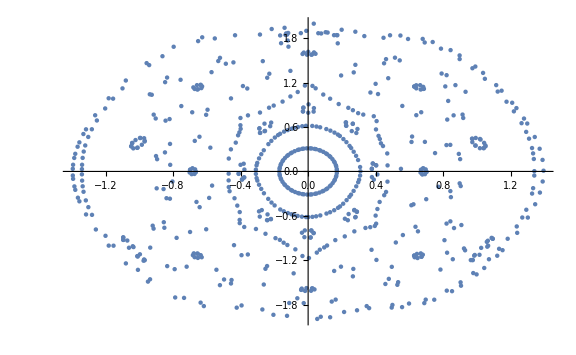
{9.76482,-Graphics-}

NumSteps = 206040

```mathematica
θ = 180
ϵ = -3
numIterations = 100
numCrossings = 70
Δt = 0.005
traj = 10
Δθ =180.0/traj
F=25
b =Cos[ (π/180)*θ]   //N
vu = √(2*(b+1))
vv = √(2*(1-b))


(* Functions for calculating position *)
calculateU = Function[{y,z}, √(√(y^2+z^2)+z)]
calculateV = Function[{y,z}, √(√(y^2+z^2)-z)]
calculateP = Function[{u,v}, u*v]
calculateR = Function[{u,v}, (u^2+v^2)/2]
calculateZ = Function[{u,v}, (u^2-v^2)/2]
au = Function[ {u,v}, (2 E^(-2/(√F (u^2+v^2))) u)/(√F)+(8 E^(-2/(√F (u^2+v^2))) u)/(√F (u^2+v^2)^2)+(4 E^(-2/(√F (u^2+v^2))) u)/(F (u^2+v^2))-2 u^3+2 u ϵ]
av = Function[ {v,u},(2 E^(-2/(√F (u^2+v^2))) v)/(√F)+(8 E^(-2/(√F (u^2+v^2))) v)/(√F (u^2+v^2)^2)+(4 E^(-2/(√F (u^2+v^2))) v)/(F (u^2+v^2))+2 v^3+2 v ϵ]



(* Default values for the loop *)

steps = 0
r = 0
uCount = 0
vCount = 0
ui = 0.00001
vi = 0.00001
t=0
posVel={}


AbsoluteTiming[ListPlot[ Part[Reap[
While[ (θ  >0 ) , 
vu = vu +(au[ui,vi] * Δt);
vv = vv + (av[vi,ui] * Δt);
uf = ui + (vu * Δt);
vf = vi + (vv * Δt);
If[ (ui * uf) < 0 || uf == 0.0001,
uCount += 1;
Sow[{vf,vv}];,
uCount+=0];
ui = uf;
vi = vf;
If[((Mod[uCount,numCrossings]==0) && (uCount ≠ 0)) || (calculateR[ui,vi] > 4 ) ,
θ =θ- Δθ;
(*Print["Angle Change.  Current angle = ", θ];*)
uCount = 0;
b =Cos[ (π/180)*θ] //N;
vu = √(2*(b+1));
vv = √(2*(1-b));
ui=0.00001;
vi =0.00001;,
t+=0];
t += Δt;
steps += 1]
],2],ImageSize->Large]]
Print["NumSteps = ", steps]
(* CoordinateTransform *)
```